```mathematica
dh[n_,k_,a_]:=dh[n,k,a]=Sum[Binomial[k,j] dh[Floor[n/(m^(k-j))],j,m+1],{m,a,n^(1/k)},{j,0,k-1}]
dh[n_,1,a_]:=Floor[n]-a+1
dh[n_,0,a_]:=1
bn[ z_, a_] := bn[z,a]=Product[ (z-k),{k,0,a-1}]/a!
dd[n_,z_]:=Sum[bn[z,a] dh[n,a,2],{a,0,Log[2,n]}]
zeros[n_] := List@@NRoots[ dd[n,z]==0,z][[All,2]]
zeros2[n_] := List@@Roots[ dd[n,z]==0,z][[All,2]]
Dp[n_, z_] := Product[1-z/k,{k,zeros[n]}]
```

```mathematica
-1/zeros[1000000]
```

{0.000884021,0.00838263,0.00558543-0.010194 ⅈ,0.00558543+0.010194 ⅈ,0.00962442-0.025014 ⅈ,0.00962442+0.025014 ⅈ,0.036726-0.0408746 ⅈ,0.036726+0.0408746 ⅈ,0.0393032-0.0768611 ⅈ,0.0393032+0.0768611 ⅈ,0.216669,0.105991-0.130723 ⅈ,0.105991+0.130723 ⅈ,0.227509-0.164963 ⅈ,0.227509+0.164963 ⅈ,0.483724-0.159633 ⅈ,0.483724+0.159633 ⅈ,1.02788,78594.}

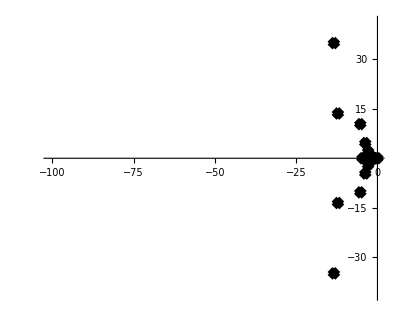

```mathematica
RootLocusPlot[1/dd[1000000,z],{k,0,1}]
```

```mathematica
zeros[30]
```

{-16.1801,-1.66598-0.772391 ⅈ,-1.66598+0.772391 ⅈ,-0.0879758}

```mathematica
pts=Table[(Point[{Re[#],Im[#]}])&/@zeros[n],{n,5,300}]
```

{{Point[{-6.70156,0}],Point[{-0.298438,0}]},{Point[{-2.,0}],Point[{-0.333333,0}]},«293»,{Point[{-227.957,0}],Point[{-11.4284,-14.0739}],Point[{-11.4284,14.0739}],Point[{-3.3017,-3.02411}],Point[{-3.3017,3.02411}],Point[{-1.28385,-0.350654}],Point[{-1.28385,0.350654}],Point[{-0.0151558,0}]}}

```mathematica
Show[Graphics[pts],Frame->True]
```

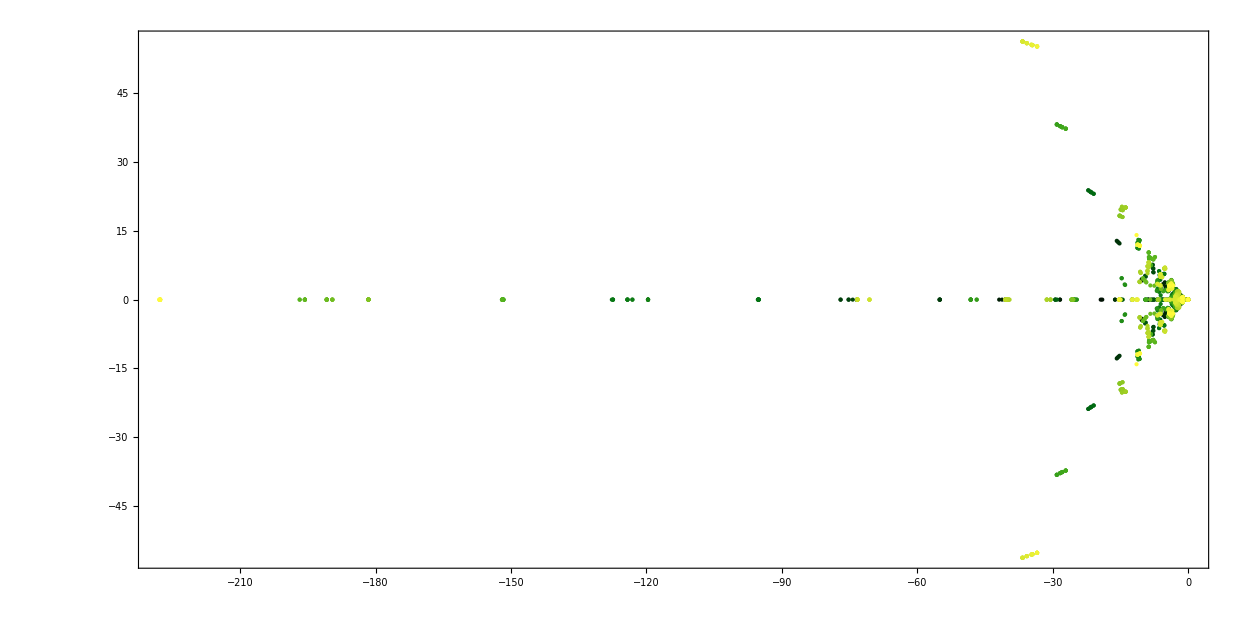

```mathematica
colfunc=ColorData["AvocadoColors"];
pts=Table[{colfunc[n/300],Point[{Re[#],Im[#]}]}&/@zeros[n],{n,5,300}];
Graphics[pts,Frame->True]
```